{h→0.002,r1→0.2,r2→0.4,R1→∞,L→0.4,Emod→200000000000,μ→0.3,ρ→1000,g→9.81}

Piecewise[{{0, 0<y<r}, {-g y ρ, -r<y<0}, {0, True}}]

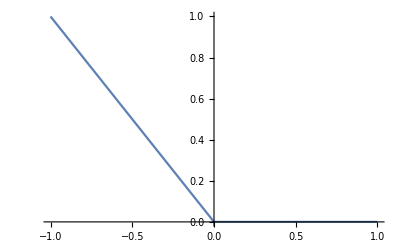

```mathematica
(*График давленьица от высоты*)
Data={h->0.002,r1->0.200,r2->0.400,R1->Infinity,L->0.400,Emod->2*10^11,μ->0.3,ρ->1000,g->9.81}
plotData={r1->1,r2->2,g->1,ρ->1,r->1,L->1};
(*Нагрузка*)
qny[y_]=Piecewise[{{0,0<y<r},{ρ*g*(-y),-r<y<0}}]
Plot[qny[y]/.plotData,{y,-r,r}/.plotData]
```

Piecewise[{{g r ρ Cos[ϕ], 0<Cos[ϕ]<1}, {0, True}}]

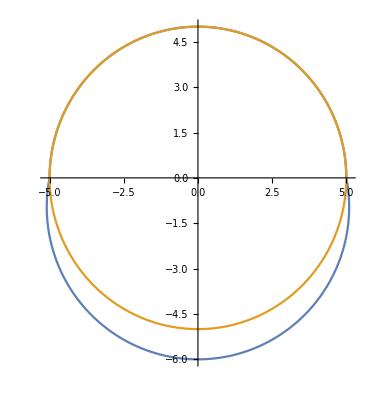

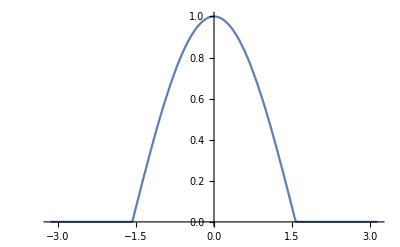

(g r ρ)/π

(g r ρ)/2

-(2 g r ρ Cos[(k π)/2])/((-1+k^2) π)

```mathematica
(*Нагрузка через угловую координату. Начало координат в нижней точке для симметрии*)
qn[ϕ_]=Simplify[qny[y]/.y->r*Cos[ϕ-Pi],Assumptions->{r>0,y>0,Element[ϕ,Reals]}]
PolarPlot[{5+qn[ϕ+Pi/2]/.plotData,5},{ϕ,0,2*Pi}]
Plot[qn[ϕ]/.plotData,{ϕ,-Pi,Pi}]
1/(2*Pi)*Integrate[qn[ϕ],{ϕ,-Pi,Pi}]
1/(Pi)*Integrate[qn[ϕ]*Cos[ϕ],{ϕ,-Pi,Pi}]
1/(Pi)*Integrate[qn[ϕ]*Cos[k*ϕ],{ϕ,-Pi,Pi}]
```

(g r ρ)/π+1/2 g r ρ Cos[ϕ]+(2 g r ρ Cos[2 ϕ])/(3 π)-(2 g r ρ Cos[4 ϕ])/(15 π)+(2 g r ρ Cos[6 ϕ])/(35 π)-(2 g r ρ Cos[8 ϕ])/(63 π)

{(2 g r ρ)/π,(g r ρ)/2,(2 g r ρ)/(3 π),0,-(2 g r ρ)/(15 π),0,(2 g r ρ)/(35 π),0}

{(g r ρ)/π,(g r ρ)/2,(2 g r ρ)/(3 π),0,-(2 g r ρ)/(15 π),0,(2 g r ρ)/(35 π),0}

{1,Cos[ϕ],Cos[2 ϕ],Cos[3 ϕ],Cos[4 ϕ],Cos[5 ϕ],Cos[6 ϕ],Cos[7 ϕ]}

{0,Sin[ϕ],Sin[2 ϕ],Sin[3 ϕ],Sin[4 ϕ],Sin[5 ϕ],Sin[6 ϕ],Sin[7 ϕ]}

(g r ρ)/π+1/2 g r ρ Cos[ϕ]+(2 g r ρ Cos[2 ϕ])/(3 π)-(2 g r ρ Cos[4 ϕ])/(15 π)+(2 g r ρ Cos[6 ϕ])/(35 π)

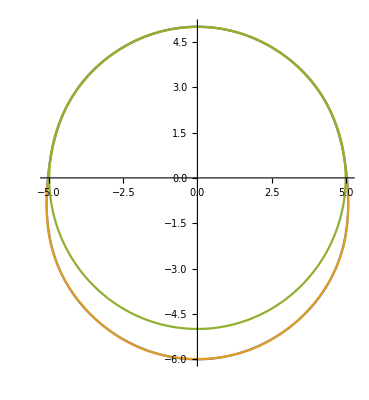

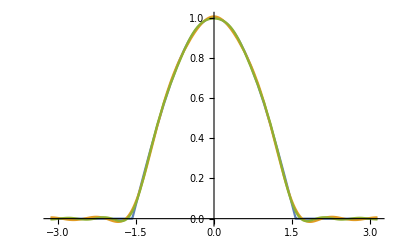

```mathematica
(*Разложим нагрузку в ряд Фурье*)
terms=8;
qnF2[ϕ_]=FourierCosSeries[qn[ϕ],ϕ,terms]
(*То же самое, но ручками*)
qnCoeffs=FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1]
qnCoeffs[[1]]=1/2*qnCoeffs[[1]];
qnCoeffs
cosines[ϕ_]=Cos[#*ϕ]&/@Range[0,terms-1]
sines[ϕ_]=Sin[#*ϕ]&/@Range[0,terms-1] (*Пригодятся потом для складывания найденных величин*)
qnF[ϕ_]=qnCoeffs.cosines[ϕ]
PolarPlot[{5+qnF[ϕ+Pi/2]/.plotData,5+qnF2[ϕ+Pi/2]/.plotData,5},{ϕ,0,2*Pi}]
Plot[{qn[ϕ]/.plotData,qnF[ϕ]/.plotData,qnF2[ϕ]/.plotData},{ϕ,-Pi,Pi}]
```

```mathematica
(*Выражаем r через r1 и r2*)
θ=Pi/2-ArcTan[(r2-r1)/L]/.Data
rData=Simplify[{r->r1+S*Sin[ArcTan[(r2-r1)/L]/.Data]},Assumptions->{r>0,r1>0,r2>0}]
rData2=Simplify[{r->r1+S*Cos[θ]},Assumptions->{r>0,r1>0,r2>0}]
Smax=L/Sin[θ]/.Data
Simplify[r/.rData/.S->Smax,Assumptions->{r>0,r1>0,r2>0}]/.Data
θ//N
```

1.10715

{r→r1+0.447214 S}

{r→r1+0.447214 S}

0.447214

0.4

1.10715

```mathematica
(*Чекаем реальную нагрузку*)
terms = 15;
coeffk=FourierCosCoefficient[qn[ϕ],ϕ,k]
coeffk/.k->2
FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1]
qnCoeffs2=FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1]/.rData/.Data/.S->Smax;
qnCoeffs2[[1]]=1/2*qnCoeffs2[[1]];
qnCoeffs2
qmax=Total[qnCoeffs2]
```

(2 g r ρ Cos[(k π)/2])/(π-k^2 π)

(2 g r ρ)/(3 π)

{(2 g r ρ)/π,(g r ρ)/2,(2 g r ρ)/(3 π),0,-(2 g r ρ)/(15 π),0,(2 g r ρ)/(35 π),0,-(2 g r ρ)/(63 π),0,(2 g r ρ)/(99 π),0,-(2 g r ρ)/(143 π),0,(2 g r ρ)/(195 π)}

{1249.05,1962.,832.699,0,-166.54,0,71.3742,0,-39.6523,0,25.2333,0,-17.4692,0,12.8107}

3929.5

```mathematica
(*Нарисуем конус и проверим*)
Xcone=r*Sin[ϕ]/.rData/.Data
Ycone=-r*Cos[ϕ]/.rData/.Data
Zcone=S*Cos[Pi/2-θ]/.rData/.Data
conePlot=ParametricPlot3D[{Xcone,Ycone,Zcone},{ϕ,-Pi,Pi},{S,0,Smax/.Data},AxesLabel->{"x","y","z"}];
waterPlot=Graphics3D[{Blue,Arrow[Tube[{{0,0,Smax/2/.Data},{0,-100,Smax/2/.Data}}]] }];
Show[{conePlot,waterPlot}]
(*Show[{waterPlot,conePlot}]*)
```

(0.2+0.447214 S) Sin[ϕ]

-(0.2+0.447214 S) Cos[ϕ]

0.894427 S

-Graphics3D-

0.31831 g r1 ρ+0.142353 g S ρ+0.5 g r1 ρ Cos[ϕ]+0.223607 g S ρ Cos[ϕ]+0.212207 g r1 ρ Cos[2 ϕ]+0.0949017 g S ρ Cos[2 ϕ]-0.0424413 g r1 ρ Cos[4 ϕ]-0.0189803 g S ρ Cos[4 ϕ]+0.0181891 g r1 ρ Cos[6 ϕ]+0.00813443 g S ρ Cos[6 ϕ]

624.524+1396.48 S+981. Cos[ϕ]+2193.58 S Cos[ϕ]+416.349 Cos[2 ϕ]+930.985 S Cos[2 ϕ]-83.2699 Cos[4 ϕ]-186.197 S Cos[4 ϕ]+35.6871 Cos[6 ϕ]+79.7987 S Cos[6 ϕ]

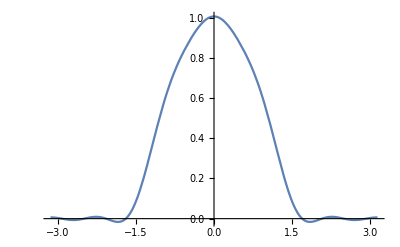

```mathematica
(*Тогда нагрузка через S и ϕ*)
q[S_,ϕ_]=Simplify[qnF[ϕ]/.rData,Assumptions->{r1>0,r2>0,S>0,L>0}]//Expand
q[S,ϕ]/.Data
Plot[qnF[ϕ]/.plotData/.S->0,{ϕ,-Pi,Pi}]
```

```mathematica
(*Матрица уравнения*)
Fk[S_]={
(*1-я*){-μ*Cos[θ]/r, -μ*k/r, -1/R1-μ*Sin[θ]/r, 0, (1-μ^2)/(Emod*h*r), 0, 0, 0},
(*2-я*){k/r, Cos[θ]/r, 0, 0, 0, 2*(1+μ)/(Emod*h*r), 0, 0},
(*3-я*){1/R1, 0, 0, -1, 0, 0, 0, 0},
(*4-я*){0, -μ*k/r^2*Sin[θ],μ*k^2/r^2, -μ*Cos[θ]/r , 0, 0, 0, 12*(1-μ^2)/(Emod*h^3*r)},
(*5-я*){Emod*h/r*(Cos[θ]^2+k^2*h^2*Sin[θ]^2/(6*(1+μ)*r^2))(*|*), k*Emod*h/r*Cos[θ](*|*), Emod*h/r*Sin[θ]*Cos[θ]*(1-k^2*h^2/(6*(1+μ)*r^2))(*|*), -k^2*Emod*h^3/(6*(1+μ)*r^2)*Sin[θ](*|*), μ/r*Cos[θ], -k/r, -1/R1, 0},
(*6-я*){Emod*h/r*k*Cos[θ](*|*), k^2*Emod*h/r(*|*), Emod*h/r*k*Sin[θ]*(1+k^2*h^2/(12*r^2))(*|*), Emod*h^3/(12*r^2)*k*Sin[θ]*Cos[θ], μ*k/r, -Cos[θ]/r, 0, μ*k/r^2*Sin[θ]},
(*7-я*) {k*Emod*h/r*Cos[θ]*Sin[θ]*(1-k^2*h^2/(6*(1+μ)*r^2))(*|*),Emod*h/r*k*Sin[θ]*(1+k^2*h^2/(12*r^2))(*|*),Emod*h/r*(Sin[θ]^2+k^4*h^2/(12*r^2)+k^2*h^2*Cos[θ]^2/(6*(1+μ)*r^2))(*|*),(3+μ)/(1+μ)*Emod*h^3/(12*r^2)*k^2*Cos[θ](*|*), 1/R1+μ*Sin[θ]/r, 0,0, μ*k^2/r^2},
(*8-я*){-k^2*Emod*h^3/(6*(1+μ)*r^2)*Sin[θ](*|*),Emod*h^3/(12*r^2)*k*Sin[θ]*Cos[θ](*|*),(3+μ)/(1+μ)*Emod*h^3/(12*r^2)*k^2*Cos[θ](*|*), Emod*h^3/(12*r)*(Cos[θ]^2+2*k^2/(1+μ))(*|*), 0, 0, 1, μ*Cos[θ]/r}
}/.rData/.Data//N;
Fk[S]/.k->1/.Data//MatrixForm;
Fk[S]/.k->1/.S->(Smax/2)/.Data//N//MatrixForm
```

(-0.447214 | -1. | -0.894427 | 0. | 7.58333×10^-9 | 0. | 0. | 0.
3.33333 | 1.49071 | 0. | 0. | 0. | 2.16667×10^-8 | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | -2.98142 | 3.33333 | -0.447214 | 0. | 0. | 0. | 0.02275
2.66673×10^8 | 5.96285×10^8 | 5.3333×10^8 | -2038.58 | 0.447214 | -3.33333 | 0. | 0.
5.96285×10^8 | 1.33333×10^9 | 1.19257×10^9 | 592.593 | 1. | -1.49071 | 0. | 2.98142
5.3333×10^8 | 1.19257×10^9 | 1.06667×10^9 | 1681.83 | 0.894427 | 0. | 0. | 3.33333
-2038.58 | 592.593 | 1681.83 | 772.65 | 0. | 0. | 1. | 0.447214)

```mathematica
(*Диффура численно решены в программе на python и записаны в .csv*)
(*Считываем их*)
harm0=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic0.csv", "Data"][[2;;-1]]
harm1=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic1.csv", "Data"][[2;;-1]];
harm2=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic2.csv", "Data"][[2;;-1]];
harm4=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic4.csv", "Data"][[2;;-1]];
harm6=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic6.csv", "Data"][[2;;-1]];
harm8=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic8.csv", "Data"][[2;;-1]];
harm10=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic10.csv", "Data"][[2;;-1]];
harm12=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic12.csv", "Data"][[2;;-1]];
harm14=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic14.csv", "Data"][[2;;-1]];
harm16=Import["C:\\Учеба\\Строймех 4 сем\\Godunov-Orthogonalization\\prog\\out\\harmonic16.csv", "Data"][[2;;-1]];
harmList={{harm0,0},{harm1,1},{harm2,2},{harm4,4},{harm6,6},{harm8,8},{harm10,10},{harm12,12},{harm14,14},{harm16,16}};
Spoints=harmList[[1,1]][[All,1]];
```

```mathematica
(*Листы с данными*)
UList={(#)[[1,All,2]],(#)[[2]]}&/@harmList
VList={(#)[[1,All,3]],(#)[[2]]}&/@harmList;
WList={(#)[[1,All,4]],(#)[[2]]}&/@harmList;
θ1List={(#)[[1,All,5]],(#)[[2]]}&/@harmList;
rT1List={(#)[[1,All,6]],(#)[[2]]}&/@harmList;
rS1ZList={(#)[[1,All,7]],(#)[[2]]}&/@harmList;
rM1List={(#)[[1,All,9]],(#)[[2]]}&/@harmList;
```

```mathematica
(*Листы с интерполированными функциями*)
UInterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@UList
VInterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@VList;
WInterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@WList;
θ1InterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@θ1List;
rT1InterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@rT1List;
rS1ZInterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@rS1ZList;
rM1InterpList={(Interpolation[Partition[Riffle[Spoints,(#)[[1]]],2],InterpolationOrder->1])[x],(#)[[2]]}&/@rM1List;
```

```mathematica
(*Суммарные функции*)
Usum[x_,ϕ_]=Total[(#[[1]])*Cos[(#[[2]])*ϕ]&/@UInterpList];
Vsum[x_,ϕ_]=Total[(#[[1]])*Sin[(#[[2]])*ϕ]&/@VInterpList];
Wsum[x_,ϕ_]=-Total[(#[[1]])*Cos[(#[[2]])*ϕ]&/@WInterpList];
θ1sum[x_,ϕ_]=Total[(#[[1]])*Cos[(#[[2]])*ϕ]&/@θ1InterpList];
T1sum[x_,ϕ_]=1/r*Total[(#[[1]])*Cos[(#[[2]])*ϕ]&/@rT1InterpList]/.rData/.Data;
S1Zsum[x_,ϕ_]=1/r*Total[(#[[1]])*Sin[(#[[2]])*ϕ]&/@rS1ZInterpList]/.rData/.Data;
M1sum[x_,ϕ_]=1/r*Total[(#[[1]])*Cos[(#[[2]])*ϕ]&/@rM1InterpList]/.rData/.Data;
```

ReplaceAll::reps: {rData} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Data} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rData} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Data} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rData} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Data} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Модуль полных перемещений*)
TotalDisp[S_,ϕ_]=Sqrt[Usum[S,ϕ]^2+Vsum[S,ϕ]^2+Wsum[S,ϕ]^2];
(*Максимальное значение*)
Plot[TotalDisp[S,0],{S,0,Smax},GridLines->Automatic]
Plot[TotalDisp[S,Pi/2],{S,0,Smax},GridLines->Automatic]
TotalDisp[0.381,0]
TotalDisp[Smax/2,Pi/2]
```

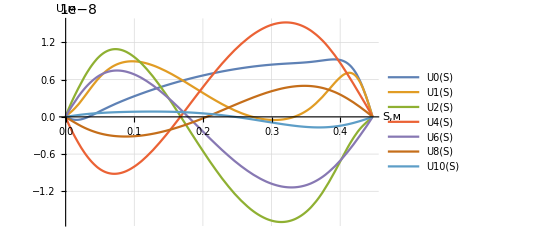

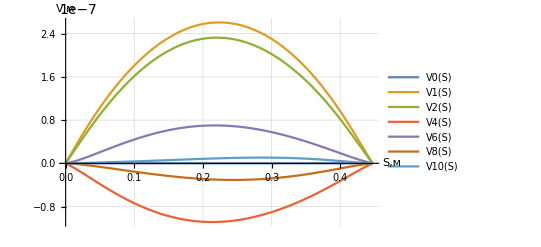

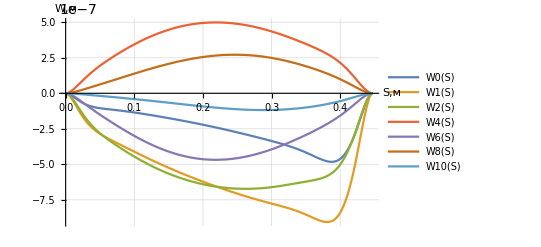

```mathematica
(*Екоторые графики*)
Plot[UInterpList[[All,1]],{x,0,Smax}]
```

```mathematica
(*Матрица поворота для преобразования координат*)
(*Сначала поворот вокруг оси X на угол Pi-θ, потом поворот вокруг Z на угол ϕ*)
Tmatr1[ϕ_]={{1,0,0},{0,Cos[Pi-θ],-Sin[Pi-θ]},{0,Sin[Pi-θ],Cos[Pi-θ]}}/.rData/.Data;
Tmatr2[ϕ_]={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}/.rData/.Data;
Tmatr[ϕ_]=Tmatr2[ϕ].Tmatr1[ϕ];
Tmatr[ϕ]//MatrixForm
(*Имеем матрицу перехода из базиса XYZ в базис T1T2N. Для рисования перемещений нужна обратная*)
TmatrInv[ϕ_]=Simplify[Inverse[Tmatr[ϕ]],Assumptions->{Element[ϕ,Reals]}];
(*А вообще, матрица поворота ортогональная, так що просто возьмем транспонированную*)

TmatrInv[ϕ_]=Transpose[Tmatr[ϕ]];
TmatrInv[ϕ]//MatrixForm
```

(Cos[ϕ] | 0.+0.447214 Sin[ϕ] | 0.+0.894427 Sin[ϕ]
Sin[ϕ] | 0.-0.447214 Cos[ϕ] | 0.-0.894427 Cos[ϕ]
0 | 0.894427 | -0.447214)

(Cos[ϕ] | Sin[ϕ] | 0
0.+0.447214 Sin[ϕ] | 0.-0.447214 Cos[ϕ] | 0.894427
0.+0.894427 Sin[ϕ] | 0.-0.894427 Cos[ϕ] | -0.447214)

```mathematica
(*Просто штука, которая рисует исходный и подвижный базисы на конусе. Круто же!*)

arrowCoeff=0.2;
basBeg[S0_,ϕ0_]={Xcone,Ycone,Zcone}/.{S->S0,ϕ->ϕ0};

xArrow[S_,ϕ_]:=Graphics3D[{Red,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{1,0,0}}]}];
yArrow[S_,ϕ_]:=Graphics3D[{Green,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{0,1,0}}]}];
zArrow[S_,ϕ_]:=Graphics3D[{Blue,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{0,0,1}}]}];
drawBasisXYZ[S_,ϕ_]:={xArrow[S,ϕ],yArrow[S,ϕ],zArrow[S,ϕ]};



nArrow2[S_,ϕ_]:=Graphics3D[{Red,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{1,0,0}}]}]; (*Бывший вектор X*)
t2Arrow2[S_,ϕ_]:=Graphics3D[{Green,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{0,1,0}}]}]; (*Бывший вектор Y*)t1Arrow2[S_,ϕ_]:=Graphics3D[{Blue,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{0,0,1}}]}]; (*Бывший вектор Z*)
drawBasisT1T2N[S_,ϕ_]:={t1Arrow2[S,ϕ],t2Arrow2[S,ϕ],nArrow2[S,ϕ]};
Show[{conePlot ,drawBasisXYZ[Smax/2,0],drawBasisT1T2N[Smax/2,Pi/3](*,drawBasisT1T2N[Smax/2/.Data,Pi/3],waterPlot*)},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Нарисуем деформированную оболочку*)
dispScale=40000;
displVec[S_,ϕ_]={ Vsum[S,ϕ],Usum[S,ϕ], Wsum[S,ϕ]};
{XconeDef,YconeDef,ZconeDef}={Xcone,Ycone, Zcone}+dispScale*Tmatr[ϕ].displVec[S,ϕ];
(*Цвет от величины полного перемещения*)
TotalDispNorm[S_,ϕ_]=TotalDisp[S,ϕ]/(1.83*10^(-6));
myColor[S_,ϕ_]=RGBColor[{TotalDispNorm[S,ϕ],1-0.5*TotalDispNorm[S,ϕ],1-TotalDispNorm[S,ϕ]}];
myColor[0,0,0,3*Smax/4,0]
(*---*)
coneDefPlot=ParametricPlot3D[{XconeDef,YconeDef,ZconeDef},{S,0,Smax/.Data},{ϕ,-Pi,Pi},AxesLabel->{"x","y","z"},ColorFunction->Function[{x,y,z,S,ϕ},myColor[S,ϕ]],ColorFunctionScaling->False];
Show[coneDefPlot(*,waterPlot*)]
```

myColor[0,0,0,0.33541,0]

-Graphics3D-

```mathematica
(*Ура, напряжения*)
(*Другие силовые факторы*)
T2[S_,ϕ_]=μ*T1[S,ϕ]+Emod*h*(1/r*D[Vsum[S,ϕ],ϕ]+Cos[θ]/r*Usum[S,ϕ]+Sin[θ]/r*Wsum[S,ϕ])/.rData/.Data;
M2[S_,ϕ_]=μ*M1[S,ϕ]+(Emod*h^3)/12*(Sin[θ]/r^2*D[Vsum[S,ϕ],ϕ]-1/r^2*D[Wsum[S,ϕ],{ϕ,2}]+Cos[θ]/r*θ1[S,ϕ])/.rData/.Data;
H[S_,ϕ_]=(Emod*h^3)/(12*(1+μ))*(1/r*D[θ1[S,ϕ],ϕ]+Cos[θ]/r^2*D[Wsum[S,ϕ],ϕ]-Sin[θ]/r^2*D[Usum[S,ϕ],ϕ])/.rData/.Data;
S1[S_,ϕ_]=S1Z[S,ϕ]-2*Sin[θ]/r*H[S,ϕ]/.rData/.Data;
```

```mathematica
(*Теперь непосредственно напряжения*)
σ1внеш[S_,ϕ_]=T1[S,ϕ]/h+6*M1[S,ϕ]/h^2/.Data;
σ2внеш[S_,ϕ_]=T2[S,ϕ]/h+6*M2[S,ϕ]/h^2/.Data;
τ12внеш[S_,ϕ_]=S1[S,ϕ]/h+6*H[S,ϕ]/h^2/.Data;

σ1внутр[S_,ϕ_]=T1[S,ϕ]/h-6*M1[S,ϕ]/h^2/.Data;
σ2внутр[S_,ϕ_]=T2[S,ϕ]/h-6*M2[S,ϕ]/h^2/.Data;
τ12внутр[S_,ϕ_]=S1[S,ϕ]/h-6*H[S,ϕ]/h^2/.Data;
(*Эквивалентные*)
σэкввнеш[S_,ϕ_]=Sqrt[σ1внеш[S,ϕ]^2+σ2внеш[S,ϕ]^2-σ1внеш[S,ϕ]*σ2внеш[S,ϕ]+3*τ12внеш[S,ϕ]];
σэкввнутр[S_,ϕ_]=Sqrt[σ1внутр[S,ϕ]^2+σ2внутр[S,ϕ]^2-σ1внутр[S,ϕ]*σ2внутр[S,ϕ]+3*τ12внутр[S,ϕ]];
σэкв[S_,ϕ_]=Max[{Abs[σэкввнеш[S,ϕ]],Abs[σэкввнутр[S,ϕ]]}];
```

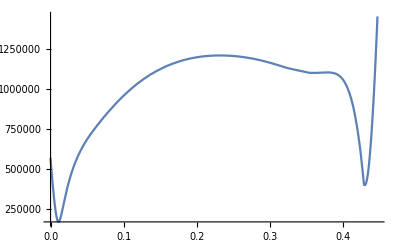

-Graphics3D-

```mathematica
Plot[σэкв[S,0],{S,0,Smax}]
Plot3D[σэкввнеш[S,ϕ],{S,0,Smax},{ϕ,-Pi,Pi}]
Plot3D[σэкввнутр[S,ϕ],{S,0,Smax},{ϕ,-Pi,Pi}]
```

```mathematica
σэквnorm[S_,ϕ_]=σэкв[S,ϕ]/(2.5*10^6);
```

```mathematica
myColor2[S_,ϕ_]=RGBColor[{σэкв[S_,ϕ_],1-0.5*σэкв[S_,ϕ_],1-σэкв[S_,ϕ_]}];
coneDefPlot2=ParametricPlot3D[{XconeDef,YconeDef,ZconeDef},{S,0,Smax/.Data},{ϕ,-Pi,Pi},AxesLabel->{"x","y","z"},ColorFunction->Function[{x,y,z,S,ϕ},myColor2[S,ϕ]],ColorFunctionScaling->False];
Show[coneDefPlot2(*,waterPlot*)]
```

Rule::rhs: Pattern S_ appears on the right-hand side of rule myColor2[S_,ϕ_]→RGBColor[{Max[√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»]),√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»])],1-0.5 Max[√Plus[«4»],√Plus[«4»]],1-Max[√Plus[«4»],√Plus[«4»]]}].

Rule::rhs: Pattern ϕ_ appears on the right-hand side of rule myColor2[S_,ϕ_]→RGBColor[{Max[√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»]),√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»])],1-0.5 Max[√Plus[«4»],√Plus[«4»]],1-Max[√Plus[«4»],√Plus[«4»]]}].

Rule::rhs: Pattern S_ appears on the right-hand side of rule myColor2[S_,ϕ_]→RGBColor[{Max[√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»]),√(Plus[«2»]^2-Plus[«2»] Plus[«2»]+Plus[«2»]^2+3 Plus[«2»])],1-0.5 Max[√Plus[«4»],√Plus[«4»]],1-Max[√Plus[«4»],√Plus[«4»]]}].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

$Aborted

Show::gtype: Symbol is not a type of graphics.

Show[coneDefPlot2]